```mathematica
Needs["PhysicalConstants`"]
ℏ=PlanckConstant/(2*Pi);
μB=1.4 *10^6;
```

```mathematica
μB/ℏ
```

(1.32755×10^40)/(Joule Second)

```mathematica
Integrate[1/(x^2+b^2)^(3/2),{x,L/2,-L/2}]
```

If[2 Im[b/L]≥1||Im[b/L]≤-1/2||Re[b/L]≠0,-(2 L)/(b^2 √(4 b^2+L^2)),Integrate[1/((b^2+x^2)^(3/2)),{x,L/2,-L/2},Assumptions→!(2 Im[b/L]≥1||Im[b/L]≤-1/2||Re[b/L]≠0)]]

```mathematica
μ0=4Pi*10^(-3);(*gauss*)
Ic=300 ;
L1=0.9;
L2=1.5;
a=0.6;
p1=Cos[ArcTan[a/(L2/2)]];
p2=Cos[ArcTan[a/(L1/2)]];
B=(2*μ0*Ic/Pi)((L1*p1/Sqrt[(L2^2/4+a^2)(4a^2+L2^2+L1^2)])+(L2*p2/Sqrt[(L1^2/4+a^2)(4a^2+L1^2+L2^2)]))
```

2.18548

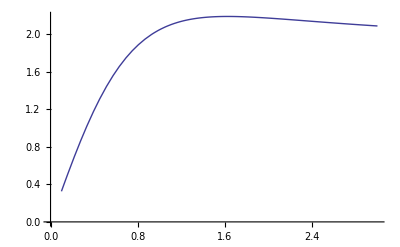

```mathematica
Plot[(2*μ0*Ic/Pi)((L1*Cos[ArcTan[a/(L2/2)]]/Sqrt[(L2^2/4+a^2)(4a^2+L2^2+L1^2)])+(L2*Cos[ArcTan[a/(L1/2)]]/Sqrt[(L1^2/4+a^2)(4a^2+L1^2+L2^2)])),{L2,0.1,3}, AxesOrigin->{0,0}]
```

```mathematica
Clear[L2,L1,a]
```

```mathematica
test=FullSimplify[(2*μ0*Ic/Pi)((L1*Cos[ArcTan[a/(L2/2)]]/Sqrt[(L2^2/4+a^2)(4a^2+L2^2+L1^2)])+(L2*Cos[ArcTan[a/(L1/2)]]/Sqrt[(L1^2/4+a^2)(4a^2+L1^2+L2^2)]))]
```

12/5 ((2 L2)/(√(1+(4 a^2)/L1^2) √((4 a^2+L1^2) (4 a^2+L1^2+L2^2)))+(2 L1)/(√(1+(4 a^2)/L2^2) √((4 a^2+L2^2) (4 a^2+L1^2+L2^2))))

```mathematica
12/5 ((2 L2)/(√(1+(4 a^2)/L1^2) √((4 a^2+L1^2) (4 a^2+L1^2+L2^2)))+(2 L1)/(√(1+(4 a^2)/L2^2) √((4 a^2+L2^2) (4 a^2+L1^2+L2^2))))/.{a->1,L1->0.5,L2->1}
```

0.455947